### Start choosing the example:

```mathematica
t=16;
beta = 0;
A =0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,3,2,S1}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15,S1->10}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 1.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.024465,Null}

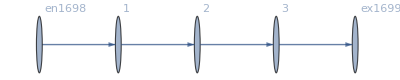

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j1700→80.,j1701→80.,j1702→80.,j1703→80.,j1704→0.,j1705→0.,j1706→0.,j1707→0.,jt1708→0.,jt1709→80.,jt1710→80.,jt1711→0.,jt1712→80.,jt1713→0.,u1714→175.,u1715→95.,u1716→15.,u1717→175.,u1718→95.,u1719→15.,u1720→15.,u1721→175.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

<|j1700→80,j1701→80,j1702→80,j1703→80,j1704→0.,j1705→0.,j1706→0.,j1707→0.,jt1708→0.,jt1709→80,jt1710→80,jt1711→0.,jt1712→80,jt1713→0.,u1714→20.1639,u1715→17.582,u1716→15.,u1717→20.1639,u1718→17.582,u1719→15.,u1720→15.,u1721→20.1639|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

<|j1700→80,j1701→80,j1702→80,j1703→80,j1704→0.,j1705→0.,j1706→0.,j1707→0.,jt1708→0.,jt1709→80,jt1710→80,jt1711→0.,jt1712→80,jt1713→0.,u1714→21.3227,u1715→18.1613,u1716→15.,u1717→21.3227,u1718→18.1613,u1719→15.,u1720→15.,u1721→21.3227|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

<|j1700→80,j1701→80,j1702→80,j1703→80,j1704→0.,j1705→0.,j1706→0.,j1707→0.,jt1708→0.,jt1709→80,jt1710→80,jt1711→0.,jt1712→80,jt1713→0.,u1714→25.0478,u1715→20.0239,u1716→15.,u1717→25.0478,u1718→20.0239,u1719→15.,u1720→15.,u1721→25.0478|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1700→80,j1701→80,j1702→80,j1703→80,j1704→0.,j1705→0.,j1706→0.,j1707→0.,jt1708→0.,jt1709→80,jt1710→80,jt1711→0.,jt1712→80,jt1713→0.,u1714→104.932,u1715→59.966,u1716→15.,u1717→104.932,u1718→59.966,u1719→15.,u1720→15.,u1721→104.932|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.20583×10^-13,ComplexInfinity]

<|j1700→80,j1701→80,j1702→80,j1703→80,j1704→0.,j1705→0.,j1706→0.,j1707→0.,jt1708→0.,jt1709→80,jt1710→80,jt1711→0.,jt1712→80,jt1713→0.,u1714→175.,u1715→95.,u1716→15.,u1717→175.,u1718→95.,u1719→15.,u1720→15.,u1721→175.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1700→80,j1701→80,j1702→80,j1703→80,j1704→0.,j1705→0.,j1706→0.,j1707→0.,jt1708→0.,jt1709→80,jt1710→80,jt1711→0.,jt1712→80,jt1713→0.,u1714→742.811,u1715→378.906,u1716→15.,u1717→742.811,u1718→378.906,u1719→15.,u1720→15.,u1721→742.811|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1700→80,j1701→80,j1702→80,j1703→80,j1704→0.,j1705→0.,j1706→0.,j1707→0.,jt1708→0.,jt1709→80,jt1710→80,jt1711→0.,jt1712→80,jt1713→0.,u1714→580101.,u1715→290058.,u1716→15.,u1717→580101.,u1718→290058.,u1719→15.,u1720→15.,u1721→580101.|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1700→80,j1701→80,j1702→80,j1703→80,j1704→0.,j1705→0.,j1706→0.,j1707→0.,jt1708→0.,jt1709→80,jt1710→80,jt1711→0.,jt1712→80,jt1713→0.,u1714→1.12074×10^19,u1715→5.6037×10^18,u1716→15.,u1717→1.12074×10^19,u1718→5.6037×10^18,u1719→15.,u1720→15.,u1721→1.12074×10^19|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1700→80,j1701→80,j1702→80,j1703→80,j1704→0.,j1705→0.,j1706→0.,j1707→0.,jt1708→0.,jt1709→80,jt1710→80,jt1711→0.,jt1712→80,jt1713→0.,u1714→4.4098×10^106,u1715→2.2049×10^106,u1716→15.,u1717→4.4098×10^106,u1718→2.2049×10^106,u1719→15.,u1720→15.,u1721→4.4098×10^106|>